```mathematica
Clear["Global`"]
```

```mathematica
λ={380,382,384,386,388,390,392,394,396,398,400,402,404,406,408,410,412,414,416,418,420,422,424,426,428,430,432,434,436,438,440,442,444,446,448,450,452,454,456,458,460,462,464,466,468,470,472,474,476,478,480,482,484,486,488,490,492,494,496,498,500,502,504,506,508,510,512,514,516,518,520,522,524,526,528,530,532,534,536,538,540,542,544,546,548,550,552,554,556,558,560,562,564,566,568,570,572,574,576,578,580,582,584,586,588,590,592,594,596,598,600,602,604,606,608,610,612,614,616,618,620,622,624,626,628,630,632,634,636,638,640,642,644,646,648,650,652,654,656,658,660,662,664,666,668,670,672,674,676,678,680,682,684,686,688,690,692,694,696,698,700,702,704,706,708,710,712,714,716,718,720,722,724,726,728,730,732,734,736,738,740,742,744,746,748,750,752,754,756,758,760,762,764,766,768,770,772,774,776,778,780,782,784,786,788,790,792,794,796,798,800,802,804,806,808,810,812,814,816,818,820,822,824,826,828,830,832,834,836,838,840,842,844,846,848,850,852,854,856,858,860,862,864,866,868,870,872,874,876,878,880,882,884,886,888,890,892,894,896,898,900,902,904,906,908,910,912,914,916,918,920,922,924,926,928,930,932,934,936,938,940,942,944,946,948,950}
```

{380,382,384,386,388,390,392,394,396,398,400,402,404,406,408,410,412,414,416,418,420,422,424,426,428,430,432,434,436,438,440,442,444,446,448,450,452,454,456,458,460,462,464,466,468,470,472,474,476,478,480,482,484,486,488,490,492,494,496,498,500,502,504,506,508,510,512,514,516,518,520,522,524,526,528,530,532,534,536,538,540,542,544,546,548,550,552,554,556,558,560,562,564,566,568,570,572,574,576,578,580,582,584,586,588,590,592,594,596,598,600,602,604,606,608,610,612,614,616,618,620,622,624,626,628,630,632,634,636,638,640,642,644,646,648,650,652,654,656,658,660,662,664,666,668,670,672,674,676,678,680,682,684,686,688,690,692,694,696,698,700,702,704,706,708,710,712,714,716,718,720,722,724,726,728,730,732,734,736,738,740,742,744,746,748,750,752,754,756,758,760,762,764,766,768,770,772,774,776,778,780,782,784,786,788,790,792,794,796,798,800,802,804,806,808,810,812,814,816,818,820,822,824,826,828,830,832,834,836,838,840,842,844,846,848,850,852,854,856,858,860,862,864,866,868,870,872,874,876,878,880,882,884,886,888,890,892,894,896,898,900,902,904,906,908,910,912,914,916,918,920,922,924,926,928,930,932,934,936,938,940,942,944,946,948,950}

```mathematica
Hg={0.001,0.001,0.001519049,0.001097004,0.001088391,0.001407078,0.002233941,0.001000301,0.001717152,0.001717152,0.00182051,0.003525916,0.028392118,0.004146064,0.003887669,0.001734378,0.002130583,0.002251168,0.003215842,0.002681826,0.003112484,0.003577595,0.002983287,0.005076285,0.005868696,0.0124147,0.015386242,0.354012755,0.801552718,0.014223465,0.004611174,0.004016866,0.00383599,0.003715405,0.003370879,0.002854089,0.004094385,0.003586208,0.0033192,0.002983287,0.003991027,0.003284747,0.003112484,0.003680953,0.003887669,0.00383599,0.002767957,0.004146064,0.003069418,0.003474237,0.002940221,0.002957447,0.003844603,0.004197743,0.004921248,0.006471618,0.006781692,0.004232195,0.004042706,0.004318327,0.00435278,0.004275261,0.003887669,0.00367234,0.003887669,0.003715405,0.004094385,0.003844603,0.003801537,0.004042706,0.0039738,0.003784311,0.004102998,0.003887669,0.004792051,0.004533656,0.004249422,0.005222709,0.004611174,0.004878182,0.011897911,0.011846232,0.258923433,0.833283612,0.021716917,0.006945342,0.005024606,0.004146064,0.003422558,0.003198616,0.003930735,0.003629274,0.00367234,0.003284747,0.002699052,0.003069418,0.002940221,0.00481789,0.174428301,0.182869201,0.014016749,0.003801537,0.002897155,0.003422558,0.004318327,0.00367234,0.002750731,0.003543142,0.002509563,0.002647373,0.002681826,0.002681826,0.003844603,0.002699052,0.002078904,0.004921248,0.004559495,0.002681826,0.002552628,0.001562115,0.00182051,0.00212197,0.002165036,0.001689355,0.001923867,0.002380365,0.002208102,0.002423431,0.001768831,0.001906641,0.001992773,0.002509563,0.002811023,0.002647373,0.002165036,0.002509563,0.003069418,0.002423431,0.002233941,0.002552628,0.002595694,0.001949707,0.002380365,0.003026352,0.003474237,0.002767957,0.001648246,0.00263876,0.002035839,0.001949707,0.00182051,0.001560157,0.001648246,0.002509563,0.001562115,0.002940221,0.001906641,0.007548263,0.1221464,0.004301101,0.001346786,0.001734378,0.001260654,0.052207515,0.004059932,0.001432917,0.001777444,0.009055567,0.001346786,0.001217588,0.001777444,0.001432917,0.001217588,0.024989919,0.005696433,0.001260654,0.001215631,0.002380365,0.010907397,0.093809093,0.002897155,0.00182051,0.002337299,0.002466497,0.012328569,0.176064802,0.033473884,0.002208102,0.002251168,0.002724892,0.004318327,0.302419907,0.213273668,0.004318327,0.00160518,0.006213223,0.147426034,0.007031473,0.002632608,0.001,0.001,0.001,0.00130372,0.001,0.001,0.001475983,0.001346786,0.083694779,0.007203737,0.002294233,0.1052646,0.05039875,0.002595694,0.001562115,0.008495711,0.274642456,0.186056072,0.004318327,0.001,0.001,0.00104141,0.001215631,0.00525347,0.081707599,0.003930735,0.001043367,0.001449696,0.001475983,0.001,0.001648246,0.077677869,0.15323992,0.008581843,0.002041991,0.001562115,0.0039738,0.046824288,0.002226559,0.001,0.001217588,0.001,0.001,0.001,0.006902276,0.001863575,0.001,0.001,0.001,0.001,0.001,0.00108056,0.001,0.001,0.001,0.001,0.00108056,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001174522,0.006176309,0.14613406,0.0102368,0.001,0.001,0.001174522,0.021569262,0.002891003,0.001,0.001,0.001,0.001,0.001228215,0.001215631,0.001,0.001,0.001,0.001,0.001,0.001,0.001}
```

{0.001,0.001,0.00151905,0.001097,0.00108839,0.00140708,0.00223394,0.0010003,0.00171715,0.00171715,0.00182051,0.00352592,0.0283921,0.00414606,0.00388767,0.00173438,0.00213058,0.00225117,0.00321584,0.00268183,0.00311248,0.0035776,0.00298329,0.00507629,0.0058687,0.0124147,0.0153862,0.354013,0.801553,0.0142235,0.00461117,0.00401687,0.00383599,0.00371541,0.00337088,0.00285409,0.00409439,0.00358621,0.0033192,0.00298329,0.00399103,0.00328475,0.00311248,0.00368095,0.00388767,0.00383599,0.00276796,0.00414606,0.00306942,0.00347424,0.00294022,0.00295745,0.0038446,0.00419774,0.00492125,0.00647162,0.00678169,0.0042322,0.00404271,0.00431833,0.00435278,0.00427526,0.00388767,0.00367234,0.00388767,0.00371541,0.00409439,0.0038446,0.00380154,0.00404271,0.0039738,0.00378431,0.004103,0.00388767,0.00479205,0.00453366,0.00424942,0.00522271,0.00461117,0.00487818,0.0118979,0.0118462,0.258923,0.833284,0.0217169,0.00694534,0.00502461,0.00414606,0.00342256,0.00319862,0.00393074,0.00362927,0.00367234,0.00328475,0.00269905,0.00306942,0.00294022,0.00481789,0.174428,0.182869,0.0140167,0.00380154,0.00289716,0.00342256,0.00431833,0.00367234,0.00275073,0.00354314,0.00250956,0.00264737,0.00268183,0.00268183,0.0038446,0.00269905,0.0020789,0.00492125,0.0045595,0.00268183,0.00255263,0.00156212,0.00182051,0.00212197,0.00216504,0.00168936,0.00192387,0.00238037,0.0022081,0.00242343,0.00176883,0.00190664,0.00199277,0.00250956,0.00281102,0.00264737,0.00216504,0.00250956,0.00306942,0.00242343,0.00223394,0.00255263,0.00259569,0.00194971,0.00238037,0.00302635,0.00347424,0.00276796,0.00164825,0.00263876,0.00203584,0.00194971,0.00182051,0.00156016,0.00164825,0.00250956,0.00156212,0.00294022,0.00190664,0.00754826,0.122146,0.0043011,0.00134679,0.00173438,0.00126065,0.0522075,0.00405993,0.00143292,0.00177744,0.00905557,0.00134679,0.00121759,0.00177744,0.00143292,0.00121759,0.0249899,0.00569643,0.00126065,0.00121563,0.00238037,0.0109074,0.0938091,0.00289716,0.00182051,0.0023373,0.0024665,0.0123286,0.176065,0.0334739,0.0022081,0.00225117,0.00272489,0.00431833,0.30242,0.213274,0.00431833,0.00160518,0.00621322,0.147426,0.00703147,0.00263261,0.001,0.001,0.001,0.00130372,0.001,0.001,0.00147598,0.00134679,0.0836948,0.00720374,0.00229423,0.105265,0.0503988,0.00259569,0.00156212,0.00849571,0.274642,0.186056,0.00431833,0.001,0.001,0.00104141,0.00121563,0.00525347,0.0817076,0.00393074,0.00104337,0.0014497,0.00147598,0.001,0.00164825,0.0776779,0.15324,0.00858184,0.00204199,0.00156212,0.0039738,0.0468243,0.00222656,0.001,0.00121759,0.001,0.001,0.001,0.00690228,0.00186358,0.001,0.001,0.001,0.001,0.001,0.00108056,0.001,0.001,0.001,0.001,0.00108056,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.00117452,0.00617631,0.146134,0.0102368,0.001,0.001,0.00117452,0.0215693,0.002891,0.001,0.001,0.001,0.001,0.00122822,0.00121563,0.001,0.001,0.001,0.001,0.001,0.001,0.001}

```mathematica
H1={0.005564756,0.006184889,0.007528511,0.010215755,0.00994014,0.008768777,0.009285555,0.010284658,0.014349976,0.01564192,0.01648599,0.017192253,0.019112943,0.032695583,0.027889551,0.045640863,0.020292919,0.021309248,0.028302973,0.030180598,0.034349271,0.02628754,0.021869091,0.022928485,0.025572664,0.028974784,0.065020025,0.208968441,0.027476128,0.029405432,0.03367746,0.039138078,0.038896915,0.038578235,0.038896915,0.037760004,0.034555982,0.034788532,0.049284145,0.04641603,0.027372773,0.070661515,0.039517048,0.043134491,0.042454067,0.027166062,0.034659338,0.025512373,0.025658794,0.031455316,0.035046921,0.029078139,0.221948173,0.995297323,0.042540197,0.030955765,0.078275372,0.044564243,0.042255969,0.032764486,0.050214345,0.035348375,0.031300283,0.03646806,0.033522427,0.027209127,0.020706341,0.021610702,0.023161035,0.022204996,0.021782961,0.024168751,0.018466971,0.032178805,0.022558128,0.024323785,0.020809697,0.020577147,0.024272107,0.029879144,0.030438987,0.039103626,0.021395378,0.022876807,0.022471998,0.025400405,0.023807007,0.028070423,0.01796742,0.015969213,0.022342804,0.023910363,0.024108461,0.026132506,0.047423746,0.039740985,0.062134683,0.041739192,0.063168239,0.077508818,0.101168622,0.088490344,0.047966362,0.064477409,0.083925474,0.04856927,0.085923681,0.078111726,0.084269993,0.064994186,0.057828203,0.117257633,0.049172177,0.072280751,0.077508818,0.039008883,0.086388781,0.044219724,0.0463299,0.04193729,0.02881975,0.054167694,0.021136989,0.023893137,0.02489224,0.022084415,0.035865152,0.014505009,0.017088898,0.015796953,0.018466971,0.020749406,0.0154955,0.013884876,0.011318214,0.025314275,0.040430022,0.399332104,1,0.267381542,0.017907129,0.013514519,0.008475937,0.007528511,0.008975488,0.009208038,0.00662415,0.006494956,0.004944623,0.004729299,0.007270122,0.006839474,0.006107372,0.003997197,0.004513975,0.006322696,0.003781873,0.004212521,0.003265095,0.003704356,0.003652678,0.004341715,0.005762854,0.002403799,0.003523484,0.005848983,0.00322203,0.00447091,0.007873029,0.009897075,0.007399316,0.010413853,0.017304222,0.016830509,0.015237111,0.017088898,0.010758371,0.016184537,0.010456918,0.007873029,0.006236567,0.006882539,0.014892592,0.012868547,0.007916094,0.008475937,0.017261157,0.011576603,0.009251103,0.012265639,0.01441888,0.004772363,0.009724816,0.009251103,0.009595621,0.005892048,0.005935113,0.003824938,0.003135901,0.004126391,0.005848983,0.002446864,0.002360734,0.001628633,0.001973151,0.003824938,0.003911067,0.003283552,0.003437354,0.003911067,0.002662188,0.002532994,0.002102345,0.001511742,0.002360734,0.001272369,0.002403799,0.001450501,0.00162248,0.001,0.00106879,0.002059281,0.002656036,0.002791382,0.001,0.001,0.001807044,0.003911067,0.002446864,0.001,0.001179528,0.001,0.001,0.001,0.001,0.001105982,0.002920577,0.002914425,0.001456373,0.001,0.001,0.001,0.001,0.003523484,0.001,0.001,0.001456373,0.001,0.001063757,0.002871639,0.00435402,0.001,0.001,0.002274605,0.005203011,0.006310392,0.001,0.001,0.00101398,0.001,0.001111855,0.001464763,0.001,0.001,0.001456373,0.001,0.001499438,0.001,0.001930086,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001}
```

{0.00556476,0.00618489,0.00752851,0.0102158,0.00994014,0.00876878,0.00928556,0.0102847,0.01435,0.0156419,0.016486,0.0171923,0.0191129,0.0326956,0.0278896,0.0456409,0.0202929,0.0213092,0.028303,0.0301806,0.0343493,0.0262875,0.0218691,0.0229285,0.0255727,0.0289748,0.06502,0.208968,0.0274761,0.0294054,0.0336775,0.0391381,0.0388969,0.0385782,0.0388969,0.03776,0.034556,0.0347885,0.0492841,0.046416,0.0273728,0.0706615,0.039517,0.0431345,0.0424541,0.0271661,0.0346593,0.0255124,0.0256588,0.0314553,0.0350469,0.0290781,0.221948,0.995297,0.0425402,0.0309558,0.0782754,0.0445642,0.042256,0.0327645,0.0502143,0.0353484,0.0313003,0.0364681,0.0335224,0.0272091,0.0207063,0.0216107,0.023161,0.022205,0.021783,0.0241688,0.018467,0.0321788,0.0225581,0.0243238,0.0208097,0.0205771,0.0242721,0.0298791,0.030439,0.0391036,0.0213954,0.0228768,0.022472,0.0254004,0.023807,0.0280704,0.0179674,0.0159692,0.0223428,0.0239104,0.0241085,0.0261325,0.0474237,0.039741,0.0621347,0.0417392,0.0631682,0.0775088,0.101169,0.0884903,0.0479664,0.0644774,0.0839255,0.0485693,0.0859237,0.0781117,0.08427,0.0649942,0.0578282,0.117258,0.0491722,0.0722808,0.0775088,0.0390089,0.0863888,0.0442197,0.0463299,0.0419373,0.0288198,0.0541677,0.021137,0.0238931,0.0248922,0.0220844,0.0358652,0.014505,0.0170889,0.015797,0.018467,0.0207494,0.0154955,0.0138849,0.0113182,0.0253143,0.04043,0.399332,1,0.267382,0.0179071,0.0135145,0.00847594,0.00752851,0.00897549,0.00920804,0.00662415,0.00649496,0.00494462,0.0047293,0.00727012,0.00683947,0.00610737,0.0039972,0.00451398,0.0063227,0.00378187,0.00421252,0.0032651,0.00370436,0.00365268,0.00434172,0.00576285,0.0024038,0.00352348,0.00584898,0.00322203,0.00447091,0.00787303,0.00989708,0.00739932,0.0104139,0.0173042,0.0168305,0.0152371,0.0170889,0.0107584,0.0161845,0.0104569,0.00787303,0.00623657,0.00688254,0.0148926,0.0128685,0.00791609,0.00847594,0.0172612,0.0115766,0.0092511,0.0122656,0.0144189,0.00477236,0.00972482,0.0092511,0.00959562,0.00589205,0.00593511,0.00382494,0.0031359,0.00412639,0.00584898,0.00244686,0.00236073,0.00162863,0.00197315,0.00382494,0.00391107,0.00328355,0.00343735,0.00391107,0.00266219,0.00253299,0.00210235,0.00151174,0.00236073,0.00127237,0.0024038,0.0014505,0.00162248,0.001,0.00106879,0.00205928,0.00265604,0.00279138,0.001,0.001,0.00180704,0.00391107,0.00244686,0.001,0.00117953,0.001,0.001,0.001,0.001,0.00110598,0.00292058,0.00291443,0.00145637,0.001,0.001,0.001,0.001,0.00352348,0.001,0.001,0.00145637,0.001,0.00106376,0.00287164,0.00435402,0.001,0.001,0.00227461,0.00520301,0.00631039,0.001,0.001,0.00101398,0.001,0.00111186,0.00146476,0.001,0.001,0.00145637,0.001,0.00149944,0.001,0.00193009,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001}

```mathematica
H2={0.005043043,0.004164562,0.005206682,0.005973199,0.005766498,0.004939693,0.004836342,0.004603803,0.006696654,0.007110057,0.006283251,0.006903355,0.006972256,0.009332096,0.008246914,0.012225915,0.00607655,0.006197126,0.007988537,0.007833511,0.008195239,0.006593303,0.005594247,0.004836342,0.005895686,0.00607655,0.015154184,0.03212092,0.006489953,0.006972256,0.007161732,0.007316758,0.007265083,0.007230633,0.008556966,0.006972256,0.006903355,0.007015319,0.00907372,0.009125395,0.005973199,0.013776175,0.008350265,0.007213407,0.007790449,0.005921524,0.006498565,0.004267913,0.005077493,0.006231576,0.006713879,0.005559797,0.045556508,0.249622418,0.007101444,0.006240189,0.014758007,0.007833511,0.008350265,0.006498565,0.009280421,0.006972256,0.004732991,0.006713879,0.006334927,0.005378933,0.00375116,0.00486218,0.004474614,0.004474614,0.004388489,0.005508121,0.004216238,0.006438277,0.004043987,0.004948305,0.004732991,0.004216238,0.004991368,0.005981812,0.00688613,0.009280421,0.005895686,0.006800005,0.005163619,0.005206682,0.004474614,0.005120556,0.003544458,0.003311919,0.004732991,0.004422939,0.004388489,0.004646866,0.008298589,0.008091888,0.010718718,0.007523459,0.011623036,0.013948426,0.01682502,0.017135072,0.009943588,0.011864188,0.016273817,0.009340709,0.014758007,0.015111122,0.01493887,0.012535967,0.009254583,0.021053785,0.009082332,0.012794344,0.013345548,0.008565579,0.016256592,0.009168458,0.00873783,0.007876574,0.006128225,0.008953144,0.00563731,0.004646866,0.004784667,0.004646866,0.006369377,0.00301048,0.002924354,0.00378561,0.003742547,0.00378561,0.002838229,0.001890848,0.001417157,0.005766498,0.004043987,0.149725377,0.967599563,0.034360185,0.002450664,0.003354982,0.001718596,0.001718596,0.002097549,0.001976973,0.001718596,0.001201843,0.00115878,0.001188141,0.001580796,0.001976973,0.001374094,0.001,0.001890848,0.001589408,0.001,0.001374094,0.00146022,0.001,0.001145079,0.001201843,0.001890848,0.001244906,0.001,0.001201843,0.001632471,0.001188141,0.001331031,0.002321475,0.001503283,0.001890848,0.003053543,0.004000924,0.003096605,0.003484171,0.001890848,0.003354982,0.00270904,0.001503283,0.001589408,0.001847785,0.002493727,0.002278413,0.002450664,0.001976973,0.003268857,0.00378561,0.002192287,0.002364538,0.00256615,0.001890848,0.00179102,0.002407601,0.002407601,0.001,0.002192287,0.001,0.001484827,0.00101589,0.001446518,0.001,0.001,0.001201843,0.001,0.001244906,0.001115718,0.001263361,0.001145079,0.00131733,0.001,0.001,0.001331031,0.001,0.001287969,0.001,0.001045251,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001102016,0.001,0.001417157,0.001,0.001029592,0.001,0.001,0.001,0.001,0.001,0.001,0.001331031,0.001,0.001,0.001,0.001055318,0.001,0.001,0.001331031,0.001,0.001,0.001,0.001,0.001,0.001,0.001263361,0.001,0.001,0.001546345,0.002106162,0.001890848,0.001,0.001,0.001,0.001067062,0.001,0.001152628,0.001503283,0.001,0.001,0.001,0.001,0.001,0.001115718,0.001,0.001,0.001,0.001103973,0.001,0.001,0.001002188,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001}
```

{0.00504304,0.00416456,0.00520668,0.0059732,0.0057665,0.00493969,0.00483634,0.0046038,0.00669665,0.00711006,0.00628325,0.00690336,0.00697226,0.0093321,0.00824691,0.0122259,0.00607655,0.00619713,0.00798854,0.00783351,0.00819524,0.0065933,0.00559425,0.00483634,0.00589569,0.00607655,0.0151542,0.0321209,0.00648995,0.00697226,0.00716173,0.00731676,0.00726508,0.00723063,0.00855697,0.00697226,0.00690336,0.00701532,0.00907372,0.0091254,0.0059732,0.0137762,0.00835027,0.00721341,0.00779045,0.00592152,0.00649857,0.00426791,0.00507749,0.00623158,0.00671388,0.0055598,0.0455565,0.249622,0.00710144,0.00624019,0.014758,0.00783351,0.00835027,0.00649857,0.00928042,0.00697226,0.00473299,0.00671388,0.00633493,0.00537893,0.00375116,0.00486218,0.00447461,0.00447461,0.00438849,0.00550812,0.00421624,0.00643828,0.00404399,0.00494831,0.00473299,0.00421624,0.00499137,0.00598181,0.00688613,0.00928042,0.00589569,0.00680001,0.00516362,0.00520668,0.00447461,0.00512056,0.00354446,0.00331192,0.00473299,0.00442294,0.00438849,0.00464687,0.00829859,0.00809189,0.0107187,0.00752346,0.011623,0.0139484,0.016825,0.0171351,0.00994359,0.0118642,0.0162738,0.00934071,0.014758,0.0151111,0.0149389,0.012536,0.00925458,0.0210538,0.00908233,0.0127943,0.0133455,0.00856558,0.0162566,0.00916846,0.00873783,0.00787657,0.00612823,0.00895314,0.00563731,0.00464687,0.00478467,0.00464687,0.00636938,0.00301048,0.00292435,0.00378561,0.00374255,0.00378561,0.00283823,0.00189085,0.00141716,0.0057665,0.00404399,0.149725,0.9676,0.0343602,0.00245066,0.00335498,0.0017186,0.0017186,0.00209755,0.00197697,0.0017186,0.00120184,0.00115878,0.00118814,0.0015808,0.00197697,0.00137409,0.001,0.00189085,0.00158941,0.001,0.00137409,0.00146022,0.001,0.00114508,0.00120184,0.00189085,0.00124491,0.001,0.00120184,0.00163247,0.00118814,0.00133103,0.00232148,0.00150328,0.00189085,0.00305354,0.00400092,0.00309661,0.00348417,0.00189085,0.00335498,0.00270904,0.00150328,0.00158941,0.00184779,0.00249373,0.00227841,0.00245066,0.00197697,0.00326886,0.00378561,0.00219229,0.00236454,0.00256615,0.00189085,0.00179102,0.0024076,0.0024076,0.001,0.00219229,0.001,0.00148483,0.00101589,0.00144652,0.001,0.001,0.00120184,0.001,0.00124491,0.00111572,0.00126336,0.00114508,0.00131733,0.001,0.001,0.00133103,0.001,0.00128797,0.001,0.00104525,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.00110202,0.001,0.00141716,0.001,0.00102959,0.001,0.001,0.001,0.001,0.001,0.001,0.00133103,0.001,0.001,0.001,0.00105532,0.001,0.001,0.00133103,0.001,0.001,0.001,0.001,0.001,0.001,0.00126336,0.001,0.001,0.00154635,0.00210616,0.00189085,0.001,0.001,0.001,0.00106706,0.001,0.00115263,0.00150328,0.001,0.001,0.001,0.001,0.001,0.00111572,0.001,0.001,0.001,0.00110397,0.001,0.001,0.00100219,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001}

```mathematica
H3={0.004464076,0.004412387,0.005411713,0.007513745,0.007910029,0.006996852,0.006996852,0.009116113,0.011752267,0.013406325,0.012820513,0.014750247,0.016740285,0.026483718,0.02260702,0.035822251,0.018265119,0.018894006,0.025811757,0.026475103,0.030980687,0.023537428,0.019453973,0.021056341,0.023589117,0.025294864,0.052707423,0.167233683,0.024467835,0.027250442,0.030877308,0.035693028,0.033410084,0.033926977,0.034082045,0.032936266,0.031807716,0.031730182,0.042662469,0.040258916,0.025501621,0.06145153,0.035322588,0.037080024,0.036985261,0.023537428,0.031428661,0.021314788,0.022986075,0.027879329,0.028714973,0.026380339,0.177235562,0.913989004,0.03629607,0.026905847,0.066801372,0.038794386,0.037493539,0.029490312,0.042920915,0.031730182,0.027465815,0.032333224,0.030360415,0.022512257,0.018471876,0.018635559,0.020918503,0.020797895,0.019281675,0.020849584,0.01747255,0.028447911,0.019626271,0.022555331,0.019402284,0.018894006,0.021469856,0.024838275,0.02595821,0.033048259,0.018506336,0.020642827,0.020487759,0.021521545,0.020797895,0.023976787,0.016352615,0.014543489,0.020875429,0.021314788,0.021736917,0.023546043,0.042352333,0.036856037,0.055248813,0.038527325,0.058565544,0.069204925,0.091818993,0.080921166,0.043489498,0.058789531,0.085917798,0.046547781,0.075743621,0.069204925,0.075838385,0.059978384,0.050596776,0.10319064,0.043532572,0.063906771,0.06623279,0.033582382,0.075640242,0.039742023,0.041809595,0.036511442,0.025708378,0.047753865,0.019970866,0.021650768,0.021211409,0.019583196,0.030179503,0.01299281,0.015939101,0.014285043,0.017127955,0.018032517,0.013294331,0.012062403,0.009719155,0.020918503,0.034099275,0.387352568,1,0.260627633,0.015964945,0.013165108,0.00674702,0.00635935,0.008185706,0.008728443,0.00674702,0.006143978,0.004980969,0.004550225,0.00710023,0.006660871,0.005713234,0.003516439,0.004765597,0.005497862,0.003990257,0.004377927,0.003947183,0.003792115,0.003645662,0.003990257,0.004851746,0.002999546,0.003516439,0.005368639,0.004033332,0.004377927,0.007479285,0.009503783,0.006833169,0.009159187,0.014672713,0.014500415,0.01376815,0.014328117,0.009503783,0.014112745,0.009719155,0.007091615,0.005454788,0.00635935,0.012648215,0.011355983,0.007350062,0.007608508,0.014931159,0.009891452,0.007910029,0.010709866,0.013251257,0.004550225,0.009288411,0.007996178,0.008900741,0.005885532,0.006014755,0.003731811,0.002987239,0.005153267,0.006143978,0.001793462,0.001879611,0.001793462,0.001750388,0.003688736,0.003516439,0.003282606,0.003774885,0.00381796,0.003214918,0.002611876,0.002396504,0.00265495,0.002181132,0.002310355,0.002224206,0.001104271,0.001805769,0.001,0.001104271,0.002094983,0.001953453,0.002138057,0.001006375,0.001264822,0.001658085,0.003947183,0.00265495,0.001061197,0.001251955,0.001276569,0.001092524,0.001215034,0.001,0.001006375,0.003731811,0.003356448,0.001491941,0.002094983,0.001,0.001061197,0.001,0.002439578,0.001,0.001,0.001276569,0.001836537,0.00143656,0.003516439,0.003799499,0.001,0.001094202,0.002525727,0.005325564,0.004759443,0.001104271,0.001,0.00212631,0.001,0.001018123,0.001473481,0.001,0.001,0.001135598,0.001,0.001535016,0.001584243,0.00157809,0.001,0.00119042,0.001,0.001178113,0.001,0.001157975,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001}
```

{0.00446408,0.00441239,0.00541171,0.00751375,0.00791003,0.00699685,0.00699685,0.00911611,0.0117523,0.0134063,0.0128205,0.0147502,0.0167403,0.0264837,0.022607,0.0358223,0.0182651,0.018894,0.0258118,0.0264751,0.0309807,0.0235374,0.019454,0.0210563,0.0235891,0.0252949,0.0527074,0.167234,0.0244678,0.0272504,0.0308773,0.035693,0.0334101,0.033927,0.034082,0.0329363,0.0318077,0.0317302,0.0426625,0.0402589,0.0255016,0.0614515,0.0353226,0.03708,0.0369853,0.0235374,0.0314287,0.0213148,0.0229861,0.0278793,0.028715,0.0263803,0.177236,0.913989,0.0362961,0.0269058,0.0668014,0.0387944,0.0374935,0.0294903,0.0429209,0.0317302,0.0274658,0.0323332,0.0303604,0.0225123,0.0184719,0.0186356,0.0209185,0.0207979,0.0192817,0.0208496,0.0174726,0.0284479,0.0196263,0.0225553,0.0194023,0.018894,0.0214699,0.0248383,0.0259582,0.0330483,0.0185063,0.0206428,0.0204878,0.0215215,0.0207979,0.0239768,0.0163526,0.0145435,0.0208754,0.0213148,0.0217369,0.023546,0.0423523,0.036856,0.0552488,0.0385273,0.0585655,0.0692049,0.091819,0.0809212,0.0434895,0.0587895,0.0859178,0.0465478,0.0757436,0.0692049,0.0758384,0.0599784,0.0505968,0.103191,0.0435326,0.0639068,0.0662328,0.0335824,0.0756402,0.039742,0.0418096,0.0365114,0.0257084,0.0477539,0.0199709,0.0216508,0.0212114,0.0195832,0.0301795,0.0129928,0.0159391,0.014285,0.017128,0.0180325,0.0132943,0.0120624,0.00971916,0.0209185,0.0340993,0.387353,1,0.260628,0.0159649,0.0131651,0.00674702,0.00635935,0.00818571,0.00872844,0.00674702,0.00614398,0.00498097,0.00455023,0.00710023,0.00666087,0.00571323,0.00351644,0.0047656,0.00549786,0.00399026,0.00437793,0.00394718,0.00379212,0.00364566,0.00399026,0.00485175,0.00299955,0.00351644,0.00536864,0.00403333,0.00437793,0.00747929,0.00950378,0.00683317,0.00915919,0.0146727,0.0145004,0.0137682,0.0143281,0.00950378,0.0141127,0.00971916,0.00709162,0.00545479,0.00635935,0.0126482,0.011356,0.00735006,0.00760851,0.0149312,0.00989145,0.00791003,0.0107099,0.0132513,0.00455023,0.00928841,0.00799618,0.00890074,0.00588553,0.00601476,0.00373181,0.00298724,0.00515327,0.00614398,0.00179346,0.00187961,0.00179346,0.00175039,0.00368874,0.00351644,0.00328261,0.00377489,0.00381796,0.00321492,0.00261188,0.0023965,0.00265495,0.00218113,0.00231036,0.00222421,0.00110427,0.00180577,0.001,0.00110427,0.00209498,0.00195345,0.00213806,0.00100638,0.00126482,0.00165809,0.00394718,0.00265495,0.0010612,0.00125196,0.00127657,0.00109252,0.00121503,0.001,0.00100638,0.00373181,0.00335645,0.00149194,0.00209498,0.001,0.0010612,0.001,0.00243958,0.001,0.001,0.00127657,0.00183654,0.00143656,0.00351644,0.0037995,0.001,0.0010942,0.00252573,0.00532556,0.00475944,0.00110427,0.001,0.00212631,0.001,0.00101812,0.00147348,0.001,0.001,0.0011356,0.001,0.00153502,0.00158424,0.00157809,0.001,0.00119042,0.001,0.00117811,0.001,0.00115798,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001}

```mathematica
Clear[x];
```

```mathematica
fH1=Interpolation[Table[{λ[[i]],H1[[i]]},{i,Length[λ]}]];
```

```mathematica
fH2=Interpolation[Table[{λ[[i]],H2[[i]]},{i,Length[λ]}]];
```

```mathematica
fH3=Interpolation[Table[{λ[[i]],H3[[i]]},{i,Length[λ]}]];
fHg=Interpolation[Table[{λ[[i]],Hg[[i]]},{i,Length[λ]}]];
```

Hydrogen Trial 1:

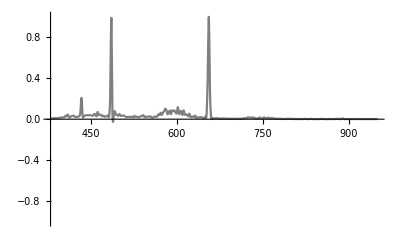

```mathematica
Plot[fH1[x],{x,380,950},PlotRange->1,PlotStyle->{Gray}]
```

Hydrogen Trial 2 :

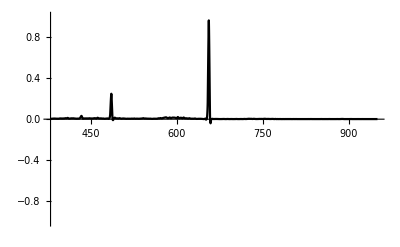

```mathematica
Plot[fH2[x],{x,380,950},PlotRange->1,PlotStyle->{Black}]
```

Hydrogen Trial 3 :

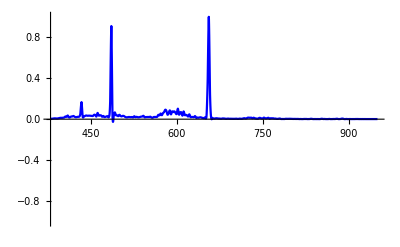

```mathematica
Plot[fH3[x],{x,380,950},PlotRange->1,PlotStyle->{Blue}]
```

Mercury Trial :

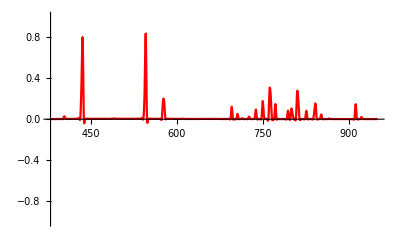

```mathematica
Plot[fHg[x],{x,380,950},PlotRange->1,PlotStyle->{Red}]
```

Finding Intensity Peaks: